```mathematica
$Assumptions={{κ1,κ2,κ3,ω1,ω2,ω3,t,z,ϵ0,μ0,ϵ,χ2,E01,E02,E03}∈Reals};
```

```mathematica
em={e->1.602176487 10^-19(*coulumbs*),c->299792458 (*m/s*),μ0->4 π 10^-7(*volt seconds / (amp meter)*),ϵ0->1/(299792458^2 4 π 10^-7)(*Farads/m*)};
```

I want to create a general model for the Nonlinear Wave equation:

∇^2 E⃗-ϵ_0 μ_0 ϵ (∂^2 E⃗)/(∂ t^2)=μ_0(∂^2 (P⃗)_nl)/(∂t^2)

We start with a couple of assumptions:

E=(Ex(t,z),Ey(t,z),0)ⅇ^(ⅈ (κ z - ω t))+ c.c.
κ=κ ẑ
P=(Px,Py,0)=χ^(1)E⃗ + χ^(2)(E⃗)^2 + χ^(3)(E⃗)^3....

However, we will ignore all susceptibilities χ^(n) for n > 2, to simplify the calculations.  We will also assume that there is no E field in the z direction (the direction of propogation), and initially, we will assume that the incident E field doesn’t change amplitude (its a CW wave, thus it changes with position, but not with time).  We also assume that the envelope is real.  With these assumptions, we can write down the twoi equations that equation 1 represents:

```mathematica
E1[t_,z_]:=E01[z] ⅇ^(ⅈ(κ1 z - ω1 t))+E01[z] ⅇ^(-ⅈ(κ1 z - ω1 t))
E2[t_,z_]:=E02[z] ⅇ^(ⅈ(κ2 z - ω2 t))+E02[z] ⅇ^(-ⅈ(κ2 z - ω2 t))
E3[t_,z_]:=E03[z] ⅇ^(ⅈ(κ3 z - ω3 t))+E03[z] ⅇ^(-ⅈ(κ3 z - ω3 t))
```

```mathematica
eq1=D[D[(E1[t,z]), z], z]-ϵ0 μ0 ϵ D[D[(E1[t,z]), t], t]==μ0 D[D[(χ2 E3[t,z]E2[t,z]), t], t]
eq2=D[D[(E2[t,z]), z], z]-ϵ0 μ0 ϵ D[D[(E2[t,z]), t], t]==μ0 D[D[(χ2 E3[t,z] E1[t,z]), t], t]
eq3=D[D[(E3[t,z]), z], z]-ϵ0 μ0 ϵ D[D[(E3[t,z]), t], t]==μ0 D[D[(χ2 E1[t,z] E2[t,z]), t], t]
initial={E01[0]==1,E02[0]==1,E03[0]==0,E01'[0]==0,E02'[0]==0,E03'[0]==0};
```

-ⅇ^(-ⅈ (z κ1-t ω1)) κ1^2 E01[z]-ⅇ^(ⅈ (z κ1-t ω1)) κ1^2 E01[z]-ϵ ϵ0 μ0 (-ⅇ^(-ⅈ (z κ1-t ω1)) ω1^2 E01[z]-ⅇ^(ⅈ (z κ1-t ω1)) ω1^2 E01[z])-2 ⅈ ⅇ^(-ⅈ (z κ1-t ω1)) κ1 E01'[z]+2 ⅈ ⅇ^(ⅈ (z κ1-t ω1)) κ1 E01'[z]+ⅇ^(-ⅈ (z κ1-t ω1)) E01''[z]+ⅇ^(ⅈ (z κ1-t ω1)) E01''[z]==μ0 (χ2 (-ⅇ^(-ⅈ (z κ2-t ω2)) ω2^2 E02[z]-ⅇ^(ⅈ (z κ2-t ω2)) ω2^2 E02[z]) (ⅇ^(-ⅈ (z κ3-t ω3)) E03[z]+ⅇ^(ⅈ (z κ3-t ω3)) E03[z])+2 χ2 (ⅈ ⅇ^(-ⅈ (z κ2-t ω2)) ω2 E02[z]-ⅈ ⅇ^(ⅈ (z κ2-t ω2)) ω2 E02[z]) (ⅈ ⅇ^(-ⅈ (z κ3-t ω3)) ω3 E03[z]-ⅈ ⅇ^(ⅈ (z κ3-t ω3)) ω3 E03[z])+χ2 (ⅇ^(-ⅈ (z κ2-t ω2)) E02[z]+ⅇ^(ⅈ (z κ2-t ω2)) E02[z]) (-ⅇ^(-ⅈ (z κ3-t ω3)) ω3^2 E03[z]-ⅇ^(ⅈ (z κ3-t ω3)) ω3^2 E03[z]))

-ⅇ^(-ⅈ (z κ2-t ω2)) κ2^2 E02[z]-ⅇ^(ⅈ (z κ2-t ω2)) κ2^2 E02[z]-ϵ ϵ0 μ0 (-ⅇ^(-ⅈ (z κ2-t ω2)) ω2^2 E02[z]-ⅇ^(ⅈ (z κ2-t ω2)) ω2^2 E02[z])-2 ⅈ ⅇ^(-ⅈ (z κ2-t ω2)) κ2 E02'[z]+2 ⅈ ⅇ^(ⅈ (z κ2-t ω2)) κ2 E02'[z]+ⅇ^(-ⅈ (z κ2-t ω2)) E02''[z]+ⅇ^(ⅈ (z κ2-t ω2)) E02''[z]==μ0 (χ2 (-ⅇ^(-ⅈ (z κ1-t ω1)) ω1^2 E01[z]-ⅇ^(ⅈ (z κ1-t ω1)) ω1^2 E01[z]) (ⅇ^(-ⅈ (z κ3-t ω3)) E03[z]+ⅇ^(ⅈ (z κ3-t ω3)) E03[z])+2 χ2 (ⅈ ⅇ^(-ⅈ (z κ1-t ω1)) ω1 E01[z]-ⅈ ⅇ^(ⅈ (z κ1-t ω1)) ω1 E01[z]) (ⅈ ⅇ^(-ⅈ (z κ3-t ω3)) ω3 E03[z]-ⅈ ⅇ^(ⅈ (z κ3-t ω3)) ω3 E03[z])+χ2 (ⅇ^(-ⅈ (z κ1-t ω1)) E01[z]+ⅇ^(ⅈ (z κ1-t ω1)) E01[z]) (-ⅇ^(-ⅈ (z κ3-t ω3)) ω3^2 E03[z]-ⅇ^(ⅈ (z κ3-t ω3)) ω3^2 E03[z]))

-ⅇ^(-ⅈ (z κ3-t ω3)) κ3^2 E03[z]-ⅇ^(ⅈ (z κ3-t ω3)) κ3^2 E03[z]-ϵ ϵ0 μ0 (-ⅇ^(-ⅈ (z κ3-t ω3)) ω3^2 E03[z]-ⅇ^(ⅈ (z κ3-t ω3)) ω3^2 E03[z])-2 ⅈ ⅇ^(-ⅈ (z κ3-t ω3)) κ3 E03'[z]+2 ⅈ ⅇ^(ⅈ (z κ3-t ω3)) κ3 E03'[z]+ⅇ^(-ⅈ (z κ3-t ω3)) E03''[z]+ⅇ^(ⅈ (z κ3-t ω3)) E03''[z]==μ0 (χ2 (-ⅇ^(-ⅈ (z κ1-t ω1)) ω1^2 E01[z]-ⅇ^(ⅈ (z κ1-t ω1)) ω1^2 E01[z]) (ⅇ^(-ⅈ (z κ2-t ω2)) E02[z]+ⅇ^(ⅈ (z κ2-t ω2)) E02[z])+2 χ2 (ⅈ ⅇ^(-ⅈ (z κ1-t ω1)) ω1 E01[z]-ⅈ ⅇ^(ⅈ (z κ1-t ω1)) ω1 E01[z]) (ⅈ ⅇ^(-ⅈ (z κ2-t ω2)) ω2 E02[z]-ⅈ ⅇ^(ⅈ (z κ2-t ω2)) ω2 E02[z])+χ2 (ⅇ^(-ⅈ (z κ1-t ω1)) E01[z]+ⅇ^(ⅈ (z κ1-t ω1)) E01[z]) (-ⅇ^(-ⅈ (z κ2-t ω2)) ω2^2 E02[z]-ⅇ^(ⅈ (z κ2-t ω2)) ω2^2 E02[z]))

These are our three equations that we need to solve, given initial conditions.  Unfortunately, they cannot be solved analytically... and χ^(2) is a matrix, that can mix the different polarizations of the E-Field.  For now we are only interested in the x-direction (assuming that χ^(2)only has elements in the x-x direction.

```mathematica
conserv={ω3->ω1+ω2,κ3->κ1+κ2};
const={ϵ->1,χ2->.0000003,κ1->(8 10^-7)^-1,ω1->(8 10^-7)^-1 c,κ2->(4 10^-7)^-1,ω2->(4 10^-7)^-1 c};
```

```mathematica
s=NDSolve[Join[{eq1,eq2,eq3},initial]/.conserv/.t->1 ω1^-1/.const/.em,{E01[z],E02[z],E03[z]},{z,0,10^-6},MaxSteps->10^6]
```

NDSolve::ndsz: At z == 4.53165×10^-9, step size is effectively zero; singularity or stiff system suspected.

{{E01[z]→InterpolatingFunction[{{0.,4.53165×10^-9}},<>][z],E02[z]→InterpolatingFunction[{{0.,4.53165×10^-9}},<>][z],E03[z]→InterpolatingFunction[{{0.,4.53165×10^-9}},<>][z]}}

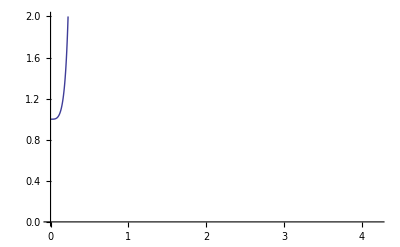

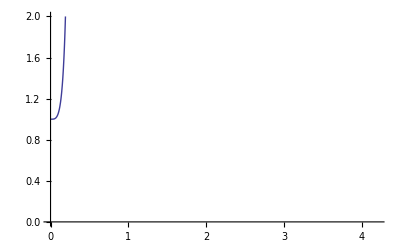

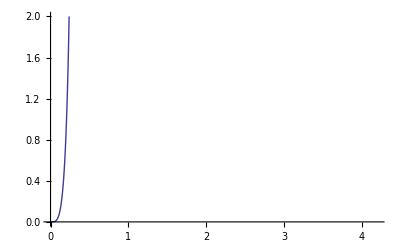

```mathematica
tfinal=42 10^-9;
Plot[(E01[z])^2/.s,{z,0,tfinal},PlotRange->{0,2}]
Plot[(E02[z])^2/.s,{z,0,tfinal},PlotRange->{0,2}]
Plot[(E03[z])^2/.s,{z,0,tfinal},PlotRange->{0,2}]
```